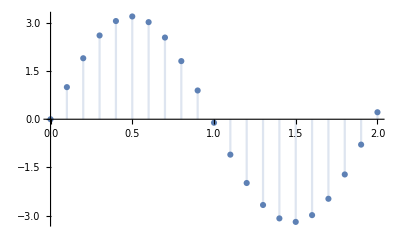

```mathematica
δ=1/10;
m=1;
g=10;
v=10;
rsol=RSolve[{m(x[t+δ]-2x[t]+x[t-δ])/δ^2==-m*g*x[t],x[0]==0,x[δ]==v*δ},x[t],t];
DiscretePlot[x[t]/.rsol,{t,0,2,δ}]
```